```mathematica
Clear["Global`*"]
c = 3 10^8;
λc = 1.55 10^-6;
ωc = c / λc 2 Pi;
Manipulate[GraphicsColumn[
{Plot[{Exp[-t^2 / T0^2],-Exp[-t^2 / T0^2],Re[Exp[-t^2 / T0^2] * Exp[I ωc t] Exp[I (α+β/T0 t +γ/T0 10^14 t^2)]]},{t,-t1,t1} , PlotRange->All , MaxRecursion->6,PlotPoints->500], 
Plot[(α+β/T0 t +γ/T0 10^14 t^2),{t,-t1,t1} ]}],
{α,0,6 Pi},{{β,0},-50,50},{{γ,0},-10,10},{T0,5 10^-15,50 10^-15},{t1,.01 *10^-12,.1 *10^-12}]
```

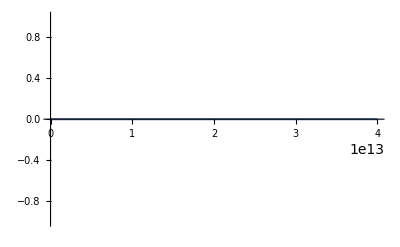

Manipulate

```mathematica
Fu = FourierTransform[field, t , ω];
Plot[Abs[Fu],{ω,0,4 10^13},PlotRange->All]
Manipulate
```

```mathematica
Plot[Arg[Exp[I (α+β/T0 t +γ/T0 10^14 t^2)]],{t,-.04 *10^-12,.04 10^-12} , PlotRange->All]
Dynamic[Plot[Arg[Exp[I (α+β/T0 t +γ/T0 10^14 t^2)]],{t,-t1,t1} , PlotRange->All,MaxRecursion->6,PlotPoints->500]]
```

-Graphics-